SIR Model

```mathematica
Needs["PlotLegends`"]
```

```mathematica
listlpcp = Partition[DeleteCases[DeleteCases[DeleteCases[DeleteCases[ReadList["/home/jhofman/Desktop/Project/LpCpK5.txt",Word],"="],"l(p)"],"c(p)"],"p"],4];
```

```mathematica
Listlp = ToExpression[Drop[listlpcp,None,-2]];
Listcp = ToExpression[Drop[Drop[listlpcp,None,{2}],None,-1]];
```

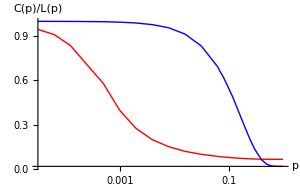

```mathematica
Liststd = ToExpression[Drop[Drop[listlpcp,None,{2}],None,{2}]];
ListLogLinearPlot[{Sort[Listlp],Sort[Listcp]},PlotRange->All,Joined->True,AxesLabel->{p,"C(p)/L(p)"},PlotLegend->{"L(p)","C(p)"},LegendShadow->None,LegendBorder->Directive[White],PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue]},ImageSize->300]
ListLogLinearPlot[Sort[Liststd],PlotRange->All,Joined->True];
```

```mathematica
f = Interpolation[Drop[Sort[Listcp],15]]
```

InterpolatingFunction[{{0.09,1.}},<>]

InterpolatingFunction::dmval: Input value {-9.210152217880013`} lies outside the range of data in the interpolating function. Extrapolation will be used.

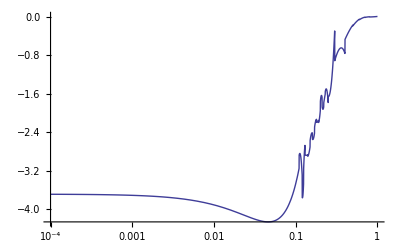

```mathematica
LogLinearPlot[f'[x],{x,10^-4,1}]
```

```mathematica
ListRh = ReadList["/home/jhofman/Desktop/Project/rhalve.txt",{Number,Number}];
ListLogLinearPlot[ListRh,Joined->True];
ListRt = ReadList["/home/jhofman/Desktop/Project/rtotal.txt",{Number,Number}];
ListLogLinearPlot[ListRt,Joined->True];
ListRh[[All,2]]=ListRh[[All,2]]*ListRt[[1,2]]/ListRh[[1,2]];
ListLogLinearPlot[{ListRt,ListRh},Joined->True,AxesLabel->{p,"# timesteps"},PlotLegend->{"r_(1/2)","r_total"},LegendShadow->None,LegendBorder->Directive[White],ImageSize->300,PlotStyle->{Directive[Thick,Green],Directive[Thick,Brown]}]
```

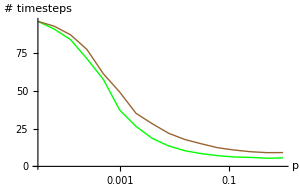

## Infected behavior as function of p

```mathematica
stream=OpenRead["/home/jhofman/Desktop/Project/SIRS2data/SIRS0.txt"];
Skip[stream,String,2]
a=ReadList[stream,{Number,Number,Number,Number}];
InfectedPlot1 = Drop[Drop[a,None,{2}],None,{3}];
SuscepPlot1 = Drop[a,None,-2];
RecoverPlot1 = Drop[Drop[a,None,{2}],None,{2}];
ListPlot[{SuscepPlot1,InfectedPlot1,RecoverPlot1},PlotRange->All,AxesLabel->{t,"# of nodes"},PlotLegend->{"susceptibles","infected","recovered"},LegendShadow->None,LegendBorder->None];
```

```mathematica
stream=OpenRead["/home/jhofman/Desktop/Project/SIRS2data/SIRS5.txt"];
Skip[stream,String,2]
a=ReadList[stream,{Number,Number,Number,Number}];
InfectedPlot2 = Drop[Drop[a,None,{2}],None,{3}];
SuscepPlot2 = Drop[a,None,-2];
RecoverPlot2 = Drop[Drop[a,None,{2}],None,{2}];
ListPlot[{SuscepPlot2,InfectedPlot2},PlotRange->All];
```

```mathematica
stream=OpenRead["/home/jhofman/Desktop/Project/SIRS2data/SIRS12.txt"];
Skip[stream,String,2]
a=ReadList[stream,{Number,Number,Number,Number}];
InfectedPlot3 = Drop[Drop[a,None,{2}],None,{3}];
SuscepPlot3 = Drop[a,None,-2];
RecoverPlot3 = Drop[Drop[a,None,{2}],None,{2}];
ListPlot[{SuscepPlot3,InfectedPlot3},PlotRange->All];
```

## Fit of infected behavior

```mathematica
Needs["PlotLegends`"]
```

20.3749

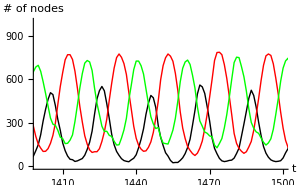

```mathematica
modlist = Drop[Drop[InfectedPlot1,1400],-2500];
modlist2 = Drop[Drop[SuscepPlot1,1400],-2500];
modlist3 = Drop[Drop[RecoverPlot1,1400],-2500];
coeff = FindFit[modlist,e+b Cos[d x + c],{{b,350},{d,1/3},c,{e,500}},x];
coeff2=FindFit[modlist2,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
coeff3=FindFit[modlist3,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
period = 2Pi/d /.coeff
Show[ListPlot[{SuscepPlot1,InfectedPlot1,RecoverPlot1},PlotRange->{{1400,1500},{0,1000}},Joined->True,AxesLabel->{t,"# of nodes"},PlotStyle->{Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Green]},ImageSize->300]]
```

22.2332

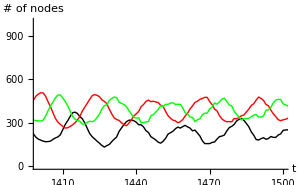

```mathematica
modlist = Drop[Drop[InfectedPlot2,1400],-2500];
modlist2 = Drop[Drop[SuscepPlot2,1400],-2500];
modlist3 = Drop[Drop[RecoverPlot2,1400],-2500];
coeff = FindFit[modlist,e+b Cos[d x + c],{{b,350},{d,1/3},c,{e,500}},x];
coeff2=FindFit[modlist2,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
coeff3=FindFit[modlist3,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
period = 2Pi/d /.coeff
Show[ListPlot[{SuscepPlot2,InfectedPlot2,RecoverPlot2},PlotRange->{{1400,1500},{0,1000}},Joined->True,AxesLabel->{t,"# of nodes"},PlotStyle->{Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Green]},ImageSize->300]]
```

```mathematica
modlist = Drop[Drop[InfectedPlot3,1400],-2500];
modlist2 = Drop[Drop[SuscepPlot3,1400],-2500];
modlist3 = Drop[Drop[RecoverPlot3,1400],-2500];
coeff = FindFit[modlist,e+b Cos[d x + c],{{b,50},{d,1/10},c,{e,400}},x];
coeff2=FindFit[modlist2,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
coeff3=FindFit[modlist3,f+g Cos[h x + i],{{g,300},{h,1/3},i,{f,500}},x];
period = 2Pi/d /.coeff
Show[ListPlot[{SuscepPlot3,InfectedPlot3,RecoverPlot3},PlotRange->{{1400,1500},{0,1000}},Joined->True,AxesLabel->{t,"# of nodes"},PlotLegend->{"susc","inf","rec"},LegendShadow->None,LegendBorder->Directive[White],PlotStyle->{Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Green]},ImageSize->300]]
Plot[e+b Cos[d x + c]/.coeff,{x,1400,1500}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

116.887

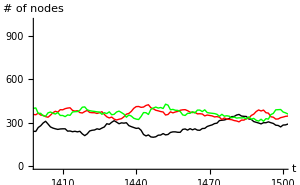

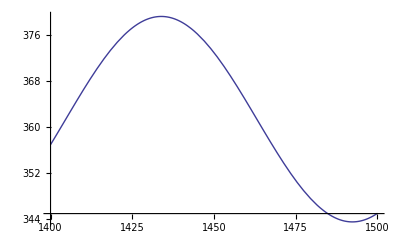

{{1/128,23.1606},{1/32,22.2332},{1/16,21.0922},{1/8,20.8592},{1/4,20.7591},{1/2,20.3807},{1,20.3749}}

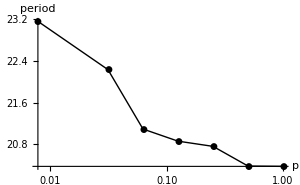

```mathematica
periods = {{2^-7,23.160576566265302},{2^-5,22.2332},{2^-4,21.0922},{2^-3,20.8592},{2^-2,20.7591},{2^-1,20.3807},{2^0,20.3749}}
ListLogLinearPlot[periods,Joined->True,PlotRange->All,AxesLabel->{p,"period"},PlotStyle->Directive[Thick,Black],PlotMarkers->Automatic,ImageSize->300]
```

## Ordering parameter as function of p

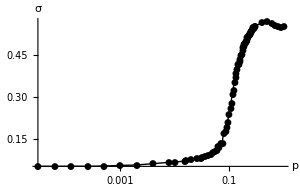

```mathematica
stream = OpenRead["/home/jhofman/Desktop/Project/sigma_test.txt"];
a = ReadList[stream,{Number,Number}];
ListLogLinearPlot[Sort[a],PlotRange->All,Joined->True,AxesLabel->{p,σ},ImageSize->300,PlotStyle->Directive[Thick,Black],PlotMarkers->Automatic]
```

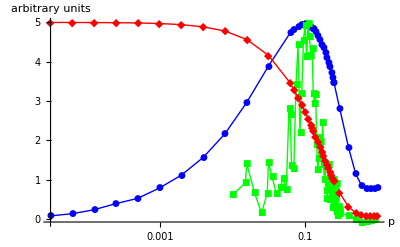

```mathematica
a =Sort[a];
tab = Table[(a[[i+1,2]]-a[[i-1,2]])/(a[[i+1,1]]-a[[i-1,1]]),{i,2,Length[a]-1}];
a2 =Drop[Drop[Drop[a,None,{2}],1],-1];
deriv =Join[a2,Partition[tab,1],2];
tab2 = Drop[Sort[Listcp],None,{1}]*5;
Listcp2 = Join[Drop[Sort[Listcp],None,{2}],tab2,2];
Liststd2 = Join[Drop[Liststd,None,{2}],(Max[Drop[Drop[deriv,None,{1}],20]]/Max[Drop[Liststd,None,{1}]])*Drop[Liststd,None,{1}],2];
ListLogLinearPlot[{Sort[Liststd2],Drop[deriv,8],Listcp2},Joined->True,PlotRange->All,ImageSize->400,PlotMarkers->Automatic,PlotStyle->{Directive[Thick,Blue],Directive[Thick,Green],Directive[Thick,Red]},PlotLegend->{"std(c_i)","σ'(p)","C(p)"},LegendShadow->None,LegendBorder->Directive[White],AxesLabel->{p,"arbitrary units"}]
```